## A366671: Smallest prime dividing 8^n+1.

### MATHEMATICA PROGRAM:

```mathematica
Table[FactorInteger[8^n+1][[1,1]],{n,0,78}] (* Paul F.Marrero Romero, Oct 20 2023 *)
```

{2,3,5,3,17,3,5,3,97,3,5,3,17,3,5,3,193,3,5,3,17,3,5,3,97,3,5,3,17,3,5,3,641,3,5,3,17,3,5,3,97,3,5,3,17,3,5,3,193,3,5,3,17,3,5,3,97,3,5,3,17,3,5,3,769,3,5,3,17,3,5,3,97,3,5,3,17,3,5}

### Formula:

a(n) = A020639(A062395(n)).  - Paul F. Marrero Romero, Oct 20 2023
a(n) = A002586(3*n) for n >= 1.  - Robert Israel, Nov 20 2023

### Plot section:

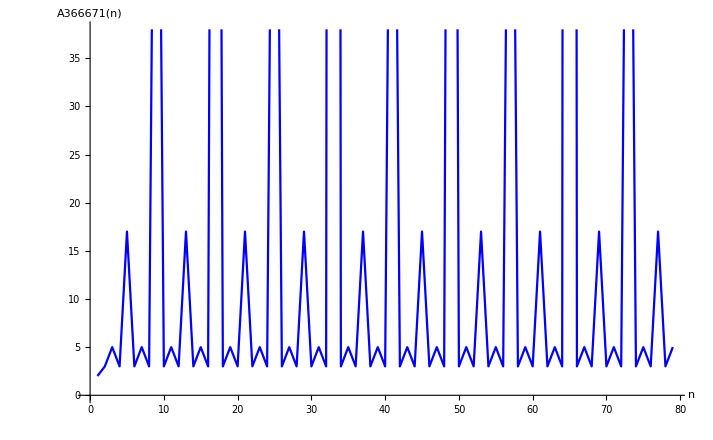

```mathematica
ListPlot[Table[FactorInteger[8^n+1][[1,1]],{n,0,78}], Joined->True, PlotStyle->Blue, AxesLabel->{"n", "A366671(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, Smallest prime dividing 8^n + 1, Entry A366671 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366671